```mathematica
Series[Exp[x]/(Exp[x]-1)^2,{x,0,10}]
```

1/x^2-1/12+x^2/240-x^4/6048+x^6/172800-x^8/5322240+(691 x^10)/118879488000+O[x]^11

```mathematica
T*D[D[-3*T*N*Exp[-h^2/i/T],T],T]
```

-(3 ⅇ^(-h^2/(i T)) h^4 N)/(i^2 T^2)

```mathematica
f[k_]:=(4*k+1)*Exp[-1/a*2*k*(2*k+1)]
```

```mathematica
Integrate[f[k],{k,0,+Infinity}]
```

ConditionalExpression[a/2,Re[1/a]>0]

```mathematica
f[0]
```

1

```mathematica
BaseForm[1,2]
```

1_2

```mathematica
D[f[k],k,k,k]
```

General::ivar: 0 is not a valid variable.

∂_(0,0,0) 1

```mathematica
(4 ⅇ^(-(2 k (1+2 k))/a)+ⅇ^(-(2 k (1+2 k))/a) (1+4 k) (-(4 k)/a-(2 (1+2 k))/a))/.{k->0}
```

4-2/a

```mathematica
D[f[s],s,s,s]
```

```mathematica
(-(96 ⅇ^(-(2 s (1+2 s))/a))/a-(24 ⅇ^(-(2 s (1+2 s))/a) (1+4 s) (-(4 s)/a-(2 (1+2 s))/a))/a+12 ⅇ^(-(2 s (1+2 s))/a) (-(4 s)/a-(2 (1+2 s))/a)^2+ⅇ^(-(2 s (1+2 s))/a) (1+4 s) (-(4 s)/a-(2 (1+2 s))/a)^3)/.(s->0)
```

-8/a^3+96/a^2-96/a

```mathematica
Series[FullSimplify[D[D[Log[1/6+x/2+1/(30*x)],x]*x^2,x]],{x,Infinity,5}]
```

1+1/(45 x^2)-8/(135 x^3)+17/(675 x^4)-4/(1215 x^5)+O[1/x]^6

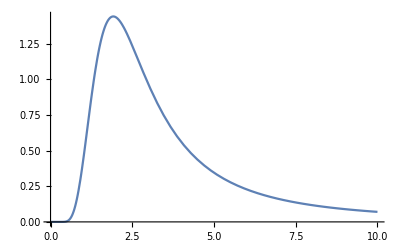

```mathematica
Plot[-(900 ⅇ^(-12/x))/((1+5 ⅇ^(-6/x))^2 x^2)+(180 ⅇ^(-6/x))/((1+5 ⅇ^(-6/x)) x^2),{x,0,10}]
```

```mathematica
D[x^2*D[Log[1+5*Exp[-6/x]],x],x]
```

```mathematica
(-(900 ⅇ^(-12/x))/((1+5 ⅇ^(-6/x))^2 x^2)+(180 ⅇ^(-6/x))/((1+5 ⅇ^(-6/x)) x^2))
```

```mathematica
g[k_]:=(4*k+3)*Exp[-1/x*(2*k+1)*(2*k+2)]
```

```mathematica
Integrate[g[s],{s,0,+Infinity}]
```

ConditionalExpression[1/2 ⅇ^(-2/x^2) x^2,Re[1/x^2]>0]

```mathematica
D[g[s],s,s,s]
```

```mathematica
(12 ⅇ^(-((1+2 s) (2+2 s))/x) (-(2 (1+2 s))/x-(2 (2+2 s))/x)^2+ⅇ^(-((1+2 s) (2+2 s))/x) (3+4 s) (-(2 (1+2 s))/x-(2 (2+2 s))/x)^3-(96 ⅇ^(-((1+2 s) (2+2 s))/x))/x-(24 ⅇ^(-((1+2 s) (2+2 s))/x) (3+4 s) (-(2 (1+2 s))/x-(2 (2+2 s))/x))/x)/.(s->0)
```

-(648 ⅇ^(-2/x))/x^3+(864 ⅇ^(-2/x))/x^2-(96 ⅇ^(-2/x))/x

```mathematica
(4 ⅇ^(-((1+2 s) (2+2 s))/x)+ⅇ^(-((1+2 s) (2+2 s))/x) (3+4 s) (-(2 (1+2 s))/x-(2 (2+2 s))/x))/.(s->0)
```

4 ⅇ^(-2/x)-(18 ⅇ^(-2/x))/x

```mathematica
FullSimplify[1/720*(-(648 ⅇ^(-2/x))/x^3+(864 ⅇ^(-2/x))/x^2-(96 ⅇ^(-2/x))/x)-1/12*(4 ⅇ^(-2/x)-(18 ⅇ^(-2/x))/x)+1/2*Exp[-2/x]+x/2*Exp[-2/x]]
```

```mathematica
Series[(ⅇ^(-2/x) (-27+x (36+x (41+5 x (1+3 x)))))/(30 x^3),{x,Infinity,5}]
```

x/2-5/6+61/(30 x)-28/(15 x^2)-41/(90 x^3)+106/(45 x^4)-112/(45 x^5)+O[1/x]^6

```mathematica
Series[Integrate[g[s],{s,0,+Infinity},Assumptions->x>0]+g[0]/2-1/12*(((D[g[s],s]))/.(s->0))+((1/720*(D[g[s],s,s,s]))/.(s->0)),{x,Infinity,5}]
```

x/2+1/6+1/(30 x)+2/(15 x^2)-161/(90 x^3)+136/(45 x^4)-124/(45 x^5)+O[1/x]^6

```mathematica
Series[3 ⅇ^(-2/x)+1/720 (-(648 ⅇ^(-2/x))/x^3+(864 ⅇ^(-2/x))/x^2-(96 ⅇ^(-2/x))/x)+1/12 (-4 ⅇ^(-2/x)+(18 ⅇ^(-2/x))/x)+1/2 ⅇ^(-2/x) x,{x,Infinity,5}]
```

x/2+5/3-89/(30 x)+47/(15 x^2)-341/(90 x^3)+181/(45 x^4)-142/(45 x^5)+O[1/x]^6

```mathematica
g[s]
```

ⅇ^(-((1+2 s) (2+2 s))/x) (3+4 s)

```mathematica
FullSimplify[D[D[Log[3*Exp[-2/x]+7*Exp[-12/x]+11*Exp[-30/x]],x]*x^2,x]]
```

(84 ⅇ^(18/x) (297+308 ⅇ^(10/x)+25 ⅇ^(28/x)))/((11+7 ⅇ^(18/x)+3 ⅇ^(28/x))^2 x^2)

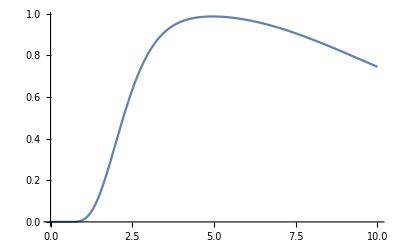

```mathematica
Plot[(84 ⅇ^(18/x) (297+308 ⅇ^(10/x)+25 ⅇ^(28/x)))/((11+7 ⅇ^(18/x)+3 ⅇ^(28/x))^2 x^2),{x,0,10}]
```

```mathematica
x
```

x